(*----------------------------*)
(*Question 1: Radial Functions*)
(*----------------------------*)

(a) Radial Wave Functions R_nl(r) through n = 2 where  0 <= l <= n-1 for n ∈ ℤ^+:

R_10(r) = 2(Z/a_0)^(3/2)e^-ρ
R_20(r) = (Z/(2 SubscriptBox[a, 0]))^(3/2)(2-ρ)e^(-ρ/2)
R_21(r) = 1/(√3)(Z/(2 SubscriptBox[a, 0]))^(3/2)ρe^(-ρ/2)

where Z is the nuclear charge and ρ = Zr/a_0 and SubscriptBox[a,0\]is the Bohr radius.

Z = 1, ρ = -r/a_0, and a_0 = 5.29E-11m = 1 bohrs

(b) Plot the corresponding radial distributions (r^2R_nl^2(r)), also in table form:

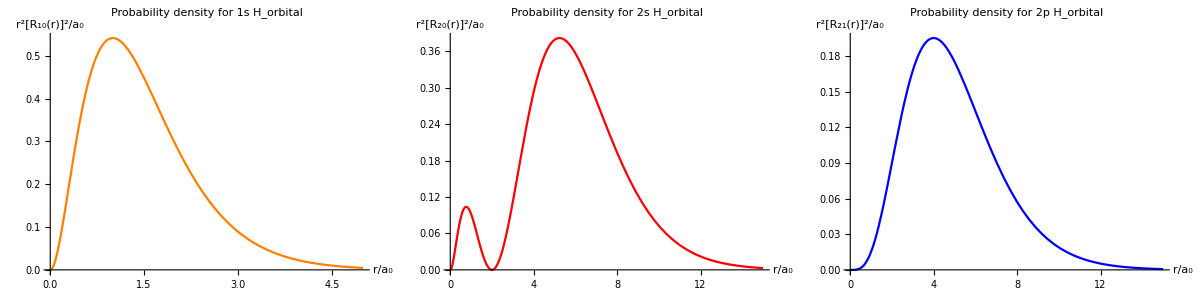

(c) Maximum probability radius for 1s state is when r = 1.

Therefore r^2[R_10(1)]^2/a_0 = 0.541341

(d) Show that 1s radial function is orthogonal to that of 2s

From Mathematica calculations, <R_10 | R_20> = 0

(*-------------------------------*)
(*Question 2: Spherical Harmonics*)
(*-------------------------------*)

Part 1 -- Table of Y_ℓ^𝓂_ℓ(θ, φ) for 0 ≤ ℓ ≤ 2 and -ℓ ≤ 𝓂_ℓ ≤ +ℓ

Y_ℓ^𝓂_ℓ(θ, φ) =  | Definition
Y_0^0(θ, φ) =  | 1/(2 √π)
Y_1^0(θ, φ) =  | 1/2 √(3/π) Cos[θ]
Y_1^1(θ, φ) =  | -1/2 ⅇ^(ⅈ φ) √(3/(2 π)) Sin[θ]
Y_1^-1(θ, φ) =  | 1/2 ⅇ^(-ⅈ φ) √(3/(2 π)) Sin[θ]
Y_2^0(θ, φ) =  | 1/4 √(5/π) (-1+3 Cos[θ]^2)
Y_2^1(θ, φ) =  | -1/2 ⅇ^(ⅈ φ) √(15/(2 π)) Cos[θ] Sin[θ]
Y_2^-1(θ, φ) =  | 1/2 ⅇ^(-ⅈ φ) √(15/(2 π)) Cos[θ] Sin[θ]
Y_2^2(θ, φ) =  | 1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2
Y_2^-2(θ, φ) =  | 1/4 ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2

Part 2 -- Visualizing the Spherical Harmonics

---------------

Y_0^0(θ, φ) plot

---------------

-Graphics3D-

----------------

Y_1^𝓂_ℓ(θ, φ) plots

----------------

{-Graphics3D-,-Graphics3D-}

----------------

Y_2^𝓂_ℓ(θ, φ) plots

----------------

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

(*------------------*)
(*Question 3: Energy*)
(*------------------*)

(a) For ψ_𝓃ℓ𝓂_ℓ(r, θ, ϕ) = R_𝓃ℓ(r)Y_ℓ^𝓂_ℓ(θ, ϕ) then for 1s function 𝓃 = 1, ℓ = 0, 𝓂_ℓ = 0

ψ_(1  s)(r, θ, ϕ) = ψ_100(r, θ, ϕ) = R_10(r)Y_0^0(θ, ϕ) = 1/(√π)(1/a_0)^(3/2)(-r/a_0)

Explanation: For the 1s function to satisfy the radial Schrodinger equation,_(rOverscriptBox[→, lim]∞)ψ_(1  s)(r, θ, ϕ) = 0.
This is because the number of radial nodes -- radial sections in the spherical coordinate plane
where R_𝓃ℓ(r) = 0 -- that is predicted from 𝓃 - ℓ - 1 should also be described by ψ_(1  s)(r, θ, ϕ). Since 𝓃, the principle
quantum number, is 1 and ℓ, the angular quantum number, is 0, 𝓃 - ℓ - 1 predicts that number of radial nodes is 0.
_(rOverscriptBox[→, lim]∞)ψ_(1  s)(r, θ, ϕ) = 0 predicts the same thing. Therefore, ψ_(1  s)(r, θ, ϕ satisfies the radial Schrodinger equation.

The energy of the electron in the 1s state is E_n = -(13.6 eV)/n^2, or simply E_1 = -13.6 eV]

(b) Deriving the energy for two trial functions ϕ_1 and ϕ_2

Part 1 --> ϵ[ϕ_1] for ϕ_1 = e^-αr

To get ϵ[ϕ_1] = (< SubscriptBox[ϕ, 1]  |  OverscriptBox[H, ^] SubscriptBox[ϕ, 1] >)/(< SubscriptBox[ϕ, 1]  |  SubscriptBox[ϕ, 1] >), I will first get < ϕ_1 | ϕ_1 >

(1) < ϕ_1 | ϕ_1 > = ∫_0^∞ r^2ϕ_1^2dr, or 1/(4 α^3)

(2) Then < ϕ | Ĥϕ > for Ĥ = (-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr) - e^2/(4 SubscriptBox[πϵ, 0] r).

(3) Substituting Ĥ into < ϕ | Ĥϕ > => 
< ϕ | (-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr) - e^2/(4 SubscriptBox[πϵ, 0] r) | ϕ >

(4) This is equivalent to: 
- < ϕ | (-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr) | ϕ > - < ϕ | e^2/(4 SubscriptBox[πϵ, 0] r) | ϕ >

(5) The left side of the equation is -∫_0^∞ r^2e^-αr((-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr)e^-αr)dr.
Integrating using mathematica, this is: ℏ^2/(2 SubscriptBox[m, e])*ConditionalExpression[-1/(4 α),Re[α]>0]

(6) The right side of the equation is -∫_0^∞ r^2e^-αr((e^2/(4 SubscriptBox[πϵ, 0] r))e^-αr)dr, or
(-1 SuperscriptBox[ℯ, 2])/(4 SubscriptBox[πϵ, 0])∫_0^∞ (re^-αr*e^-αr)dr, or -1/(4 SubscriptBox[πϵ, 0])∫_0^∞ re^(-2 αr)dr. 
Integrating using mathematica: -1/(4 SubscriptBox[πϵ, 0]) * ConditionalExpression[1/(4 α^2),Re[α]>0]

(7) Combining the results from step 1 (the denominator), step 5 and 6 (the numerator),
ϵ[ϕ_1] =([FractionBox[ℏ, 2 SubscriptBox[m, ℯ]]*FractionBox[1, 4  α]]-[FractionBox[1 SuperscriptBox[ℯ, 2], 4 SubscriptBox[πϵ, 0]]*FractionBox[1, 4 SuperscriptBox[α, 2]]])/[FractionBox[1, 4 SuperscriptBox[α, 3]]]

Part 2 --> ϵ[ϕ_2] for ϕ_1 = e^(-SuperscriptBox[αr, 2])

(1) Separating the numerator out and denominator out as before, 
the denominator is < ϕ_2 | ϕ_2 > = ∫_0^∞ r^2ϕ_2^2dr, or (√(π/2))/(8 α^(3/2))

(2) The left side of the numerator is ∫_0^∞ r^2e^(-SuperscriptBox[αr, 2])((-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr)e^(-SuperscriptBox[αr, 2]))dr,
so the result is -ℏ/m_e*ConditionalExpression[(3 √(π/2))/(16 √α),Re[α]>0]

(3) The right side of the numerator is -∫_0^∞ r^2e^(-SuperscriptBox[αr, 2])((ℯ^2/(4 SubscriptBox[πϵ, 0] r))e^(-SuperscriptBox[αr, 2]))dr, 
so the result is -ℯ^2/(4 SubscriptBox[πϵ, 0])* ConditionalExpression[1/(4 α),Re[α]>0]

(4) Putting the results of step 1, 2, and 3 together:
ϵ[ϕ_2] =(-[FractionBox[ℏ, SubscriptBox[m, e]]*FractionBox[3 SqrtBox[FractionBox[π, 2]], 16 SqrtBox[α]]] - [FractionBox[SuperscriptBox[ℯ, 2], 4 SubscriptBox[πϵ, 0]]*FractionBox[1, 4 α]])/[FractionBox[SqrtBox[FractionBox[π, 2]], 8 SuperscriptBox[α, 3/2]]]

```mathematica
(*H-Atom-M5*)
(*Jared Frazier*)
(*Description:

Reproducing radial distribution functions, spherical harmonics, and probability density functions
for the hydrogen atom from Quantum Chemistry 2nd Edition (McQuarrie).

*)
(*Date: 10/25/2020*)

Clear["Global`*"]

(*----------------------------*)
(*Question 1: Radial Functions*)
(*----------------------------*)

Print["(*----------------------------*)
(*Question 1: Radial Functions*)
(*----------------------------*)"]

(*Part a -- table form*)
Print["(a) Radial Wave Functions R_nl(r) through n = 2 where  0 <= l <= n-1 for n ∈ ℤ^+:"]
tableEle = {{"R_10(r) = 2(Z/a_0)^(3/2)e^-ρ"}, {"R_20(r) = (Z/(2 SubscriptBox[a, 0]))^(3/2)(2-ρ)e^(-ρ/2)"}, {"R_21(r) = 1/(√3)(Z/(2 SubscriptBox[a, 0]))^(3/2)ρe^(-ρ/2)"}};
Grid[tableEle, Frame->All]
Print["where Z is the nuclear charge and ρ = Zr/a_0 and SubscriptBox[a,0\]is the Bohr radius."]
a0 = 1;
Print["Z = 1, ρ = -r/a_0, and a_0 = 5.29E-11m = 1 bohrs \n"]

(*Part b -- plot radial distribution functions pg328 MQ2e*)
Print["(b) Plot the corresponding radial distributions (r^2R_nl^2(r)), also in table form:"]

(*Radial functions of r to plot for part b*)
R1s = r^2*(2/a0^(3/2)*Exp[-r/a0])^2;
R2s = r^2*(1/(2*a0^(3/2))*(2-(r/a0))*Exp[-r/(2*a0)])^2;
R2p = r^2*(1/(Sqrt[3]*(2*a0)^(3/2))*(r/a0)*Exp[-r/(2*a0)])^2;

(*Plots for each radial dist functions for table -- range for r from pg 329 in MQ2e*)
r1 = Plot[R1s, {r,0,5}, PlotRange->All, PlotStyle->{Orange}, PlotLabel->"Probability density for 1s H_orbital",
          AxesLabel->{"r/a_0","r^2[R_10(r)]^2/a_0"}, ImageSize->250];
r2 = Plot[R2s, {r,0,15}, PlotRange->All, PlotStyle->{Red}, PlotLabel->"Probability density for 2s H_orbital",
		  AxesLabel->{"r/a_0","r^2[R_20(r)]^2/a_0"}, ImageSize->250];
r3 = Plot[R2p, {r,0,15}, PlotRange->All, PlotStyle->{Blue}, PlotLabel->"Probability density for 2p H_orbital",
		  AxesLabel->{"r/a_0","r^2[R_21(r)]^2/a_0"}, ImageSize->250];
radialDistTable = {r1,r2,r3};
TableForm[radialDistTable, TableDirections->Row]

(*Part c -- max probability radius for 1s state*)
R1sFunc[r_] := r^2*(2/a0^(3/2)*Exp[-r/a0])^2;
R1sDerivative = D[R1s, {r, 1}];         (*First derivative*)
critPt = NSolve[R1sDerivative == 0, r]; (*Critical points*)
Print["\n(c) Maximum probability radius for 1s state is when r = ", r/.critPt[[2]]]
Print["Therefore r^2[R_10(1)]^2/a_0 = ", R1sFunc[r/.critPt[[2]]]]

(*Part d -- 1s wave function is orthogonal to that of of the 2s*)
Print["\n(d) Show that 1s radial function is orthogonal to that of 2s"]
R10 = 2(1/a0)^(3/2)Exp[-r/a0];
R20 = (1/(2*a0))^(3/2)*(2-(r/a0))*Exp[-r/(2*a0)];
orthogonalRadFuncs = Integrate[(r^2)*R10*R20, {r, 0, Infinity}];
Print["From Mathematica calculations, <R_10 | R_20> = ", orthogonalRadFuncs]

(*-------------------------------*)
(*Question 2: Spherical Harmonics*)
(*-------------------------------*)

(*Pg MQ2e Pg 323*)

Print["\n(*-------------------------------*)
(*Question 2: Spherical Harmonics*)
(*-------------------------------*)"]

(*Spherical Harmonic Elements of Table*)
shR1 = SphericalHarmonicY[0, 0, θ, φ];
shR2 = SphericalHarmonicY[1, 0, θ, φ];
shR3 = SphericalHarmonicY[1, 1, θ, φ];
shR4 = SphericalHarmonicY[1, -1, θ, φ];
shR5 = SphericalHarmonicY[2, 0, θ, φ];
shR6 = SphericalHarmonicY[2, 1, θ, φ];
shR7 = SphericalHarmonicY[2, -1, θ, φ];
shR8 = SphericalHarmonicY[2, 2, θ, φ];
shR9 = SphericalHarmonicY[2, -2, θ, φ];

(*Print grid -- part 1*)
Print["Part 1 -- Table of Y_ℓ^𝓂_ℓ(θ, φ) for 0 ≤ ℓ ≤ 2 and -ℓ ≤ 𝓂_ℓ ≤ +ℓ"]
Grid[
	{
		{"Y_ℓ^𝓂_ℓ(θ, φ) = ", "Definition"},
		{"Y_0^0(θ, φ) = ",  shR1},
		{"Y_1^0(θ, φ) = ", shR2},
		{"Y_1^1(θ, φ) = ", shR3},
		{"Y_1^-1(θ, φ) = ", shR4},
		{"Y_2^0(θ, φ) = ", shR5},
		{"Y_2^1(θ, φ) = ", shR6},
		{"Y_2^-1(θ, φ) = ", shR7},
		{"Y_2^2(θ, φ) = ", shR8},
		{"Y_2^-2(θ, φ) = ", shR9}
	},
	Frame->All
]

(*Print spherical plot*)
Print["Part 2 -- Visualizing the Spherical Harmonics"]
Print["---------------"]
Print["Y_0^0(θ, φ) plot"]
Print["---------------"]
SphericalPlot3D[shR1, {θ, 0, Pi}, {φ, 0, 2*Pi}]
Print["----------------"]
Print["Y_1^𝓂_ℓ(θ, φ) plots"]
Print["----------------"]
Table[
	SphericalPlot3D[
		{Abs[SphericalHarmonicY[1, m, θ, φ]]},
		{θ, 0, Pi},
		{φ, 0, 2*Pi}
	],
	{m, 0, 1}
]
Print["----------------"]
Print["Y_2^𝓂_ℓ(θ, φ) plots"]
Print["----------------"]
Table[
	SphericalPlot3D[
		{Abs[SphericalHarmonicY[2, m, θ, φ]]},
		{θ, 0, Pi},
		{φ, 0, 2*Pi}
	],
	{m, 0, 2}
]

(*------------------*)
(*Question 3: Energy*)
(*------------------*)
Print["\n(*------------------*)
(*Question 3: Energy*)
(*------------------*)"]

Print["(a) For ψ_𝓃ℓ𝓂_ℓ(r, θ, ϕ) = R_𝓃ℓ(r)Y_ℓ^𝓂_ℓ(θ, ϕ) then for 1s function 𝓃 = 1, ℓ = 0, 𝓂_ℓ = 0"]
Print["ψ_(1  s)(r, θ, ϕ) = ψ_100(r, θ, ϕ) = R_10(r)Y_0^0(θ, ϕ) = 1/(√π)(1/a_0)^(3/2)(-r/a_0)"]
Print["\tExplanation: For the 1s function to satisfy the radial Schrodinger equation,_(rOverscriptBox[→, lim]∞)ψ_(1  s)(r, θ, ϕ) = 0.
This is because the number of radial nodes -- radial sections in the spherical coordinate plane
where R_𝓃ℓ(r) = 0 -- that is predicted from 𝓃 - ℓ - 1 should also be described by ψ_(1  s)(r, θ, ϕ). Since 𝓃, the principle
quantum number, is 1 and ℓ, the angular quantum number, is 0, 𝓃 - ℓ - 1 predicts that number of radial nodes is 0.
_(rOverscriptBox[→, lim]∞)ψ_(1  s)(r, θ, ϕ) = 0 predicts the same thing. Therefore, ψ_(1  s)(r, θ, ϕ satisfies the radial Schrodinger equation."]
Print["The energy of the electron in the 1s state is E_n = -(13.6 eV)/n^2, or simply E_1 = -13.6 eV]"]
 
 Print["\n(b) Deriving the energy for two trial functions ϕ_1 and ϕ_2"]
 phi1 = Exp[-α*r];
 phi2 = Exp[-α*r^2];
 Print["Part 1 --> ϵ[ϕ_1] for ϕ_1 = e^-αr"]
 Print["To get ϵ[ϕ_1] = (< SubscriptBox[ϕ, 1]  |  OverscriptBox[H, ^] SubscriptBox[ϕ, 1] >)/(< SubscriptBox[ϕ, 1]  |  SubscriptBox[ϕ, 1] >), I will first get < ϕ_1 | ϕ_1 >"]
 Print["(1) < ϕ_1 | ϕ_1 > = ∫_0^∞ r^2ϕ_1^2dr, or ", 
 Normal[Assuming[Element[α, PositiveReals], Integrate[r^2 * phi1^2, {r, 0, Infinity}]]]
 ]
 Print["(2) Then < ϕ | Ĥϕ > for Ĥ = (-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr) - e^2/(4 SubscriptBox[πϵ, 0] r)."]
 Print["(3) Substituting Ĥ into < ϕ | Ĥϕ > => 
< ϕ | (-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr) - e^2/(4 SubscriptBox[πϵ, 0] r) | ϕ >"]
Print["(4) This is equivalent to: 
- < ϕ | (-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr) | ϕ > - < ϕ | e^2/(4 SubscriptBox[πϵ, 0] r) | ϕ >"]
lhsIntegration = Assuming[
	Element[α, PositiveReals], 
	Integrate[
		Exp[-α*r]*(-2*α*r*Exp[-α*r]+α^2*r^2*Exp[-α*r]),
		{r, 0, Infinity}]
];
Print["(5) The left side of the equation is -∫_0^∞ r^2e^-αr((-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr)e^-αr)dr.
Integrating using mathematica, this is: ℏ^2/(2 SubscriptBox[m, e])*", lhsIntegration]
rhsIntegration = Assuming[
	Element[α, PositiveReals], 
	Integrate[
		r*Exp[-2*α*r],
		{r, 0, Infinity}]
];
Print["(6) The right side of the equation is -∫_0^∞ r^2e^-αr((e^2/(4 SubscriptBox[πϵ, 0] r))e^-αr)dr, or
(-1 SuperscriptBox[ℯ, 2])/(4 SubscriptBox[πϵ, 0])∫_0^∞ (re^-αr*e^-αr)dr, or -1/(4 SubscriptBox[πϵ, 0])∫_0^∞ re^(-2 αr)dr. 
Integrating using mathematica: -1/(4 SubscriptBox[πϵ, 0]) * ", rhsIntegration]
Print["(7) Combining the results from step 1 (the denominator), step 5 and 6 (the numerator),
ϵ[ϕ_1] =([FractionBox[ℏ, 2 SubscriptBox[m, ℯ]]*FractionBox[1, 4  α]]-[FractionBox[1 SuperscriptBox[ℯ, 2], 4 SubscriptBox[πϵ, 0]]*FractionBox[1, 4 SuperscriptBox[α, 2]]])/[FractionBox[1, 4 SuperscriptBox[α, 3]]]"]

Print["\nPart 2 --> ϵ[ϕ_2] for ϕ_1 = e^(-SuperscriptBox[αr, 2])"]
Print["(1) Separating the numerator out and denominator out as before, 
the denominator is < ϕ_2 | ϕ_2 > = ∫_0^∞ r^2ϕ_2^2dr, or ", 
Normal[Assuming[Element[α, PositiveReals], Integrate[r^2 * phi2^2, {r, 0, Infinity}]]]]
lhsIntegrationPhi2 = Assuming[
	Element[α, PositiveReals], 
	Integrate[
		Exp[-α*r^2]*(3*α*r^2*Exp[-α*r^2]-2*α^2r^4*Exp[-α*r^2]),
		{r, 0, Infinity}
	]
];
Print["(2) The left side of the numerator is ∫_0^∞ r^2e^(-SuperscriptBox[αr, 2])((-SuperscriptBox[ℏ, 2])/(2 SubscriptBox[m, e] SuperscriptBox[r, 2])d/dr(r^2d/dr)e^(-SuperscriptBox[αr, 2]))dr,
so the result is -ℏ/m_e*", lhsIntegrationPhi2]
rhsIntegrationPhi2 = Assuming[
	Element[α, PositiveReals], 
	Integrate[
		r*Exp[-2*α*r^2],
		{r, 0, Infinity}]
];
Print["(3) The right side of the numerator is -∫_0^∞ r^2e^(-SuperscriptBox[αr, 2])((ℯ^2/(4 SubscriptBox[πϵ, 0] r))e^(-SuperscriptBox[αr, 2]))dr, 
so the result is -ℯ^2/(4 SubscriptBox[πϵ, 0])* ", rhsIntegrationPhi2]
Print["(4) Putting the results of step 1, 2, and 3 together:
ϵ[ϕ_2] =(-[FractionBox[ℏ, SubscriptBox[m, e]]*FractionBox[3 SqrtBox[FractionBox[π, 2]], 16 SqrtBox[α]]] - [FractionBox[SuperscriptBox[ℯ, 2], 4 SubscriptBox[πϵ, 0]]*FractionBox[1, 4 α]])/[FractionBox[SqrtBox[FractionBox[π, 2]], 8 SuperscriptBox[α, 3/2]]]"]
```